```mathematica
data = Import["/Users/AShepelev/Desktop/GR.txt","Table"];
```

```mathematica
plot = Table[{data[[i,2]] - data[[i,3]], -(data[[i,2]]+5+5Log10[data[[i,4]]/1000])},{i,1,Length@data}]
```

{{0.507,-4.15282},{0.435,-3.35525},{0.523,-4.53818},{0.537,-4.44164},{0.677,-4.9151},{0.465,-3.04206},39226,{0.53,3.71899},{0.52,2.56545},{0.23,2.70937},{0.68,0.6006},{0.68,1.28666}}
 |  |  |  |

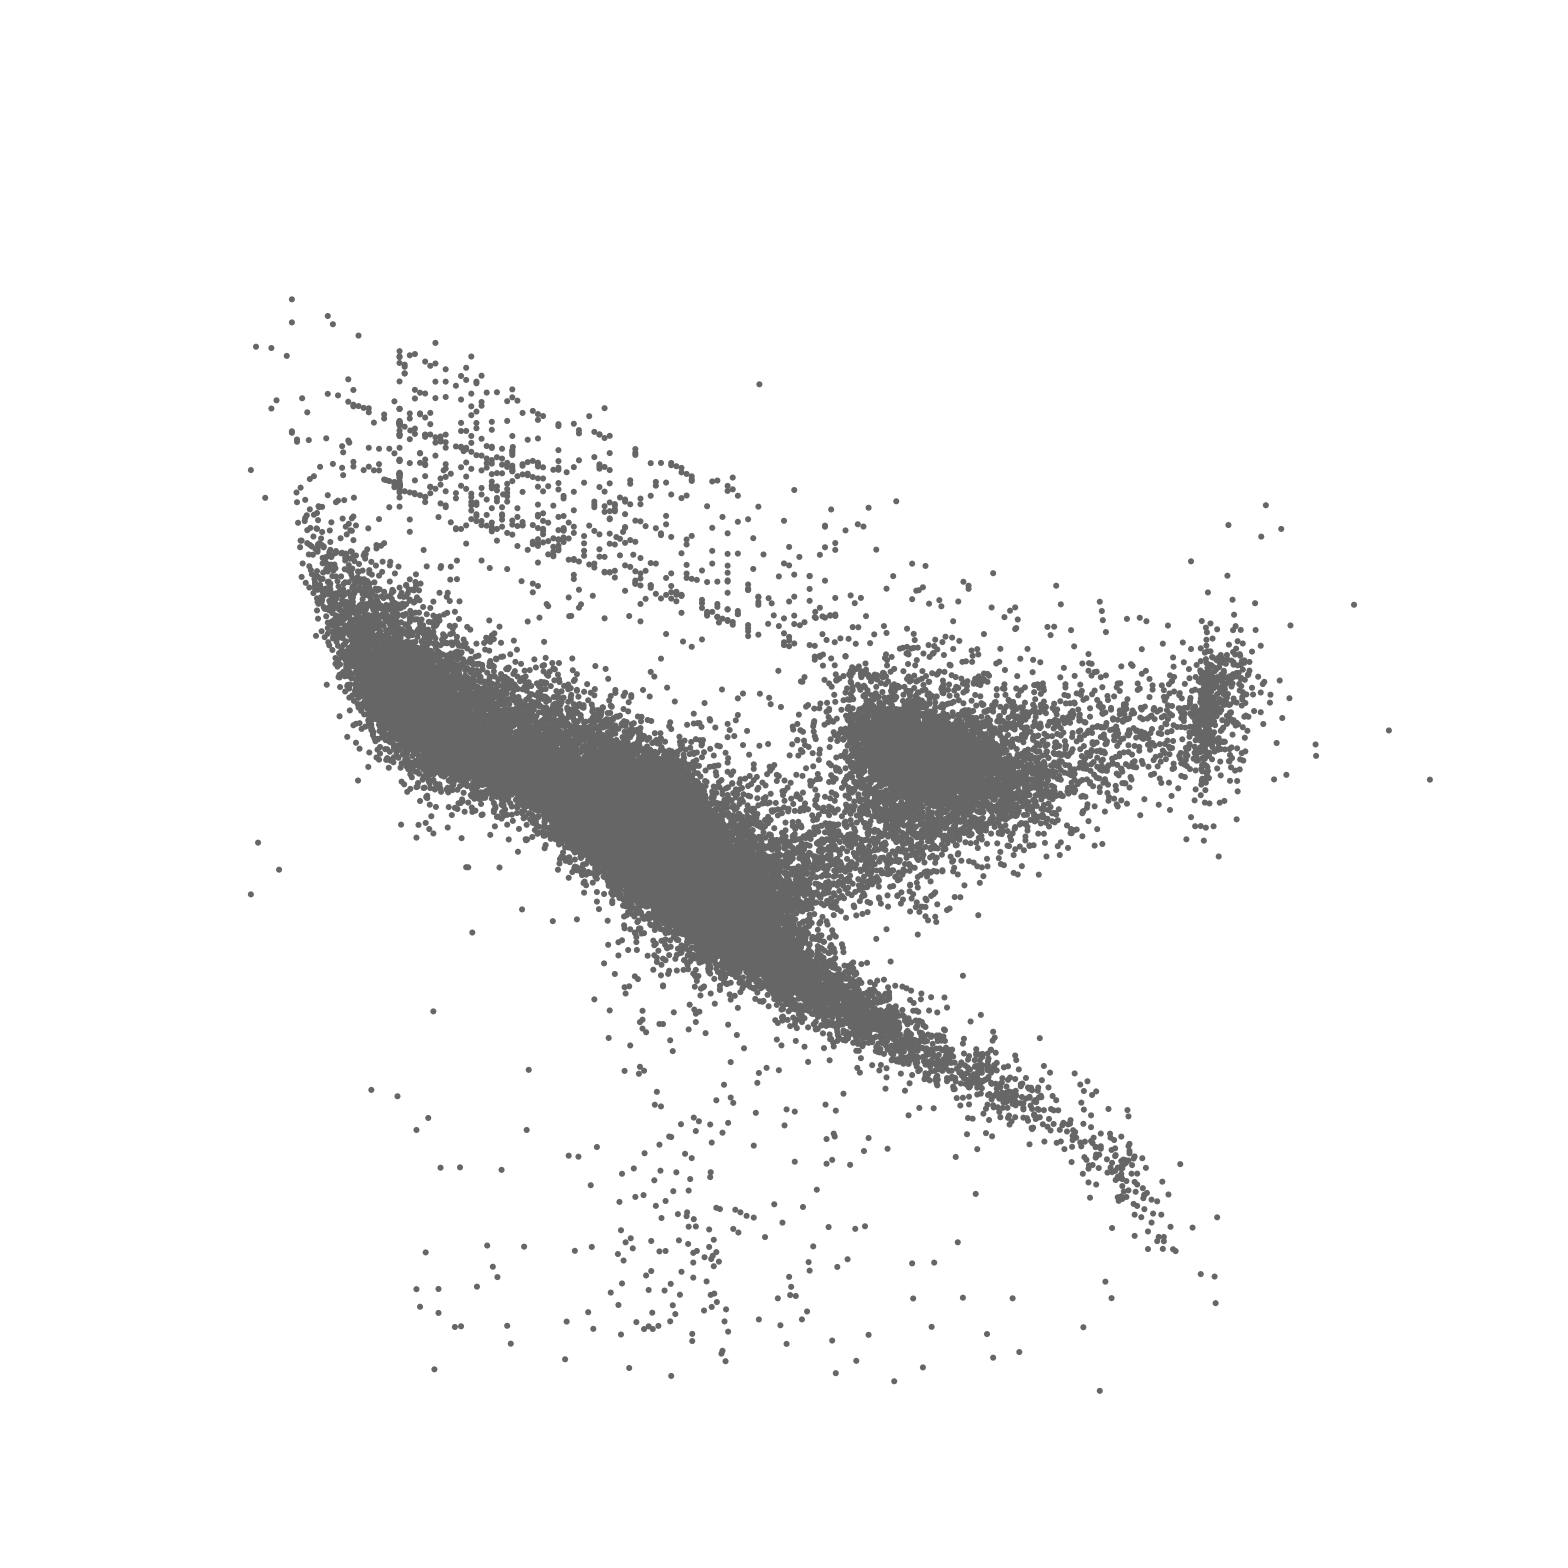

```mathematica
ListPlot[plot, AspectRatio->5/4,PlotRange->{{-0.5, 2},{-15,10}}, ImageSize->2000,PlotStyle->RGBColor[0.4,0.4,0.4], Axes->None]
```

```mathematica
tmp=Table[{Round[plot[[i,1]],0.0001],Round[-plot[[i,2]],0.0001]},{i,1,Length@plot}];
```

```mathematica
Export["/Users/AShepelev/Desktop/data.dat",tmp]
```

/Users/AShepelev/Desktop/data.dat